### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np=3
d = 1;
lm = 1;
lp[k_]:=((k+1)^(-1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
```

3

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*Define c and d of Mehler's formular, see 2.28 in Harmonium1 document; here c is c and d0 is d*)
c[s_,t_, Np_]:=Sqrt[Np/((Np-1) t^2+s^2)];
d0[s_,t_, Np_]:=Sqrt[((Np-1) s^2 +t^2)/(Np s^2 t^2)];
```

```mathematica
(*Define the q parameter in Mehler's formula, see 2.29 of Harmonium1 document*)
Q[s_,t_, Np_]:=(d0[s,t,Np]-c[s,t,Np])/(d0[s,t,Np]+c[s,t,Np]);
```

### Defining Exponential Functions, Normalization and HF Basis Functions

```mathematica
efun3[a_,b_, x1_, x2_, x3_]:=Exp[-a(x1^2+x2^2+x3^2)+b(x1+x2+x3)^2];
efun3poly[a_,b_, x1_, x2_, x3_]:=-a(x1^2+x2^2+x3^2)+b(x1+x2+x3)^2;
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
efunana2rdo[a_,b_,Np_, x1_, x1p_, x2_, x2p_]:=Exp[-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2)-4 a b (x1^2+x1p^2+x1 x2+x2^2+x1p x2p+x2p^2))];
efun2poly[a_,b_, Np_]:=-a(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2
efun1[a_,b_, x1_, x1p_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)]*Exp[b^2(Np-1)/(a-b(Np-1)) x1* x1p];
efun1poly[a_,b_]:=-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)+(b^2(Np-1)/(a-b(Np-1)) x1* x1p)
```

```mathematica
Integrate[efun3[a,b, x1, x2, x3]*efun3[a,b,x1,x2,x3],{x1,-∞,+∞},{x2,-∞,+∞},{x3,-∞,+∞}, Assumptions-> a>0 && b<0 ]
```

π^(3/2)/(2 √2 a √(a-3 b))

```mathematica
Integrate[efun1[a,b,x1,x1],{x1,-∞,+∞}, Assumptions-> a>0 && b<0 ]
```

√((a π-2 b π)/(2 a^2-6 a b))

```mathematica
Integrate[efunana2rdo[a,b,Np,x1,x1, x2, x2],{x1,-∞,+∞}, {x2,-∞,+∞},Assumptions-> a>0 && Im[a]==Im[b]==0]
```

(√((a-b)/(a-3 b)) π)/(2 a)

```mathematica
(*Integrate[efun1rdo[a,b, x1,x1, x2, x2, Np],{x1,-∞,+∞}, {x2,-∞,+∞}, Assumptions-> a>0 && b<0 && Np∈PositiveIntegers ]*)
```

```mathematica
norm2rdopre[a_,b_, Np_]:=((√((a-b)/(a-3 b)) π)/(2 a))^(-1)
norm2rdo[lm_,lp_, Np_]:=norm2rdoPre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
norm3rdopre[a_,b_, Np_]:=(π^(3/2)/(2 √2 √(a^2 (a-3 b))))^(-1)
norm3rdo[lm_,lp_, Np_]:=norm3rdoPre[A[lp],B[lm,lp, Np], Np];
norm1rdopre[a_,b_, Np_]:=(√((a π-2 b π)/(2 a^2-6 a b)))^(-1)
norm1rdo[lm_,lp_, Np_]:=norm1rdoPre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
(*define 2 particle hf basis*)
(*define 2 particle hf basis*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hf2basis[m1_, m2_, n1_,n2_,a_]:=1/2(hfcoef[m1,x1,a]*hfcoef[m2,x2, a]+hfcoef[m2,x1,a]*hfcoef[m1,x2,a])*1/2(hfcoef[n1,x1p,a]*hfcoef[n2,x2p,a]+hfcoef[n2,x1p,a]*hfcoef[n1,x2p,a])
hf3basis[m1_, m2_,m3_, n1_,n2_,n3_,a_]:=1/6*Permanent[{{hfcoef[m1,x1,a], hfcoef[m1,x2,a], hfcoef[m1,x3,a]},{hfcoef[m2,x1,a], hfcoef[m2,x2,a], hfcoef[m2,x3,a]},{hfcoef[m3,x1,a], hfcoef[m3,x2,a], hfcoef[m3,x3,a]}}]*1/6*Permanent[{{hfcoef[n1,x1p,a], hfcoef[n1,x2p,a], hfcoef[n1,x3p,a]},{hfcoef[n2,x1p,a], hfcoef[n2,x2p,a], hfcoef[n2,x3p,a]},{hfcoef[n3,x1p,a], hfcoef[n3,x2p,a], hfcoef[n3,x3p,a]}}]
hf1basis[m1_, n1_,a_]:=(hfcoef[m1,x1,a]*hfcoef[n1,x1p,a])
```

### Determining the coefficients of the Polynomial Contribution to the integral

```mathematica
(*Determine the coefficients of the polynomial 'hfibasis' by the coefficientlist function where q corresponds to the power, i.e. x^q , importantly this is not the mathematica index*)
```

```mathematica
coefstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_,q_,a_] :=CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x][[q+1]]
maxdegreestart3[m1_, m2_,m3_, n1_,n2_,n3_, x_] := Length[CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x]]-1
constantstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_] := coefstart3[m1, m2,m3, n1,n2,n3,x,1,a]

coefstart2[m1_, m2_, n1_,n2_,x_,q_,a_] :=CoefficientList[hf2basis[m1,m2,n1,n2,a], x][[q+1]]
maxdegreestart2[m1_,m2_,n1_,n2_, x_] := Length[CoefficientList[hf2basis[m1,m2,n1,n2,a], x]]-1
constantstart2[m1_, m2_, n1_,n2_,x_] := coefstart2[m1, m2, n1,n2,x,1,a]

coefstart1[m1_, n1_,x_,q_,a_] :=CoefficientList[hf1basis[m1,n1,a], x][[q+1]]
maxdegreestart1[m1_,n1_, x_] := Length[CoefficientList[hf1basis[m1,n1,a], x]]-1
constantstart1[m1_, n1_,x_] := coefstart1[m1, n1,x,1,a]
```

```mathematica
coefstart2[2,2,2,2,x1,1,a]
```

0

```mathematica
Sum[coefstart2[5,5,2,5,x1,q,a]*x1^q,{q,0,maxdegreestart2[5,5,2,5,x1]}]-hf2basis[5,5,2,5,a]//Simplify
```

0

### Integrating coefficient by coefficient and determining helper functions/exponential polynomials

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
exppolyinit3 = efun3poly[a,b,x1,x2,x3]+efun3poly[a,b,x1p,x2p,x3p]-a(x1^2+x2^2+x3^2+x1p^2+x2p^2+x3p^2)
exppolyinit2=-2a*(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2;
```

b (x1+x2+x3)^2-a (x1^2+x2^2+x3^2)+b (x1p+x2p+x3p)^2-a (x1p^2+x2p^2+x3p^2)-a (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)

```mathematica
exppolyinit1 = efun1poly[a,b]-a(x1^2+x1p^2)
```

(2 b^2 x1 x1p)/(a-2 b)-a (x1^2+x1p^2)+(-a+b+b^2/(a-2 b)) (x1^2+x1p^2)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
exppolyinit3-(Sum[efuncoef[exppolyinit3,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
int3poly[m1_,m2_,m3_,n1_,n2_,n3_]:= Sum[coefstart3[m1,m2,m3,n1,n2,n3,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]], {q,0, maxdegreestart3[m1,m2,m3,n1,n2,n3, x1]}]
int2poly[m1_,m2_,n1_,n2_]:= Sum[coefstart2[m1,m2,n1,n2,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]], {q,0, maxdegreestart2[m1,m2,n1,n2, x1]}]
int1poly[m1_,n1_]:= Sum[coefstart1[m1,n1,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]], {q,0, maxdegreestart1[m1,n1, x1]}]
```

```mathematica
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

## Running the algorithm for the various particle sectors

```mathematica
mode1 = 0;
mode2 =1;
```

### Run algorithm for 1 RDO diag mode1

```mathematica
polym1 = int1poly[mode1, mode1];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

(a (-4 a^2+12 a b-5 b^2) x1p^2)/(2 a^2-5 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)))

0

```mathematica
intd11=norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))

### Run algorithm for 1 RDO diag mode2

```mathematica
polym1 = int1poly[mode2, mode2];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

(a (-4 a^2+12 a b-5 b^2) x1p^2)/(2 a^2-5 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2))

0

```mathematica
intd12 =norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2) √((a π-2 b π)/(2 a^2-6 a b)))

```mathematica
2
```

2

### Run algorithm for 1 RDO offdiag mode1mode2

```mathematica
polym1 = int1poly[mode1, mode2];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

(a (-4 a^2+12 a b-5 b^2) x1p^2)/(2 a^2-5 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

0

0

```mathematica
into1=norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

0

### Run algorithm for 2 RDO diag mode1mode1

```mathematica
polymm1 = int2poly[mode1, mode1, mode1, mode1];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd21 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO diag mode2mode2

```mathematica
polymm1 = int2poly[mode2, mode2, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd23 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO diag mode1mode2

```mathematica
polymm1 = int2poly[mode1, mode2, mode1, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd22 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO offdiag mode1mode1mode2mode2

```mathematica
polymm1 = int2poly[mode1, mode1, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into22 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO offdiag mode1mode1mode1mode2

```mathematica
polymm1 = int2poly[mode1, mode1, mode1, mode2]
```

(√a (2 a √(2/π) x1p+2 a √(2/π) x2p))/(√2 √(2 a-b-b^2/(2 (a-b))))

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into21 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

0

### Run algorithm for 2 RDO offdiag mode1mode2mode2mode2

```mathematica
polymm1 = int2poly[mode1, mode2, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into23 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

0

### Run algorithm for 3rdo diag mode1mode1mode1

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode1, mode1, mode1]
```

(2 √2 a^(3/2))/(√(2 a-b) π)

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

a^(3/2)/(√((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(√a √(π/2))/(a-b)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(√a π)/(√2 √((a (2 a-3 b))/(a-b)) (a-b))

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

π^(3/2)/(√2 √a (2 a-3 b))

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd31= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))

### Run algorithm for 3rdo diag mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode2, mode2, mode2, mode2, mode2, mode2]
```

-(64 √2 a^(9/2) x1p x2 x2p x3 (2 b x2+2 b x3) x3p)/(√(2 a-b) (-2 a+b) π)

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(8 a^(7/2) b x1p x2p x3 (a-b+2 a b x3^2) x3p)/((a-b)^2 √((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a^(3/2) b^2 √(π/2) x3 (a-b+2 a b x3^2) x3p (a-b+2 a b x3p^2))/(a-b)^5

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

0

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

0

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd34= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

0

### Run algorithm for 3rdo diag mode1mode1mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode2, mode1, mode1, mode2]
```

-(a^(5/4) (2 b x2+2 b x3) (4 a^(5/4) (2/π)^(3/4) x1p+4 a^(5/4) (2/π)^(3/4) x2p+4 a^(5/4) (2/π)^(3/4) x3p))/(9 √(2 a-b) (-2 a+b) (2 π)^(1/4))+1/(√(2 a-b))√π (1/9 a^(5/4) (2/π)^(3/4) x2 (4 a^(5/4) (2/π)^(3/4) x1p+4 a^(5/4) (2/π)^(3/4) x2p+4 a^(5/4) (2/π)^(3/4) x3p)+1/9 a^(5/4) (2/π)^(3/4) x3 (4 a^(5/4) (2/π)^(3/4) x1p+4 a^(5/4) (2/π)^(3/4) x2p+4 a^(5/4) (2/π)^(3/4) x3p))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(4 a^(9/2) √(2/π) x3 (x1p+x2p+x3p))/(9 ((a (a-b))/(2 a-b))^(3/2) (2 a-b)^(3/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(2 a^(7/2) √(2 π) x3 x3p)/(9 (a-b)^3)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

0

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

0

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd32= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

0

### Run algorithm for 3rdo diag mode1mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode2, mode2, mode1, mode2, mode2]
```

(2 2^(3/4) a^(7/4) x2 x3 (8 a^(7/4) (2/π)^(3/4) x1p x2p+8 a^(7/4) (2/π)^(3/4) x1p x3p+8 a^(7/4) (2/π)^(3/4) x2p x3p))/(9 √(2 a-b) π^(1/4))-1/(2 √(2 a-b) (-2 a+b))√π (2 b x2+2 b x3) (2/9 a^(7/4) (2/π)^(3/4) x2 (8 a^(7/4) (2/π)^(3/4) x1p x2p+8 a^(7/4) (2/π)^(3/4) x1p x3p+8 a^(7/4) (2/π)^(3/4) x2p x3p)+2/9 a^(7/4) (2/π)^(3/4) x3 (8 a^(7/4) (2/π)^(3/4) x1p x2p+8 a^(7/4) (2/π)^(3/4) x1p x3p+8 a^(7/4) (2/π)^(3/4) x2p x3p))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(2 a^(5/2) b (a-b+8 a^2 x3^2-6 a b x3^2) (x2p x3p+x1p (x2p+x3p)))/(9 (a-b)^2 √((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(√a b^2 √(π/2) (a-b+8 a^2 x3^2-6 a b x3^2) (a-b+8 a^2 x3p^2-6 a b x3p^2))/(36 (a-b)^5)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(a^(3/2) b^2 π (a-b+8 a^2 x3p^2-6 a b x3p^2))/(6 √2 ((a (2 a-3 b))/(a-b))^(3/2) (a-b)^4)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(b^2 π^(3/2))/(√2 √a (2 a-3 b)^3)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd33= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)

### Run algorithm for 3rdo offdiag mode1mode1mode1mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode2, mode2, mode2]
```

(16 √2 a^3 x1p x2p x3p)/(√(2 a-b) π)

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(8 a^3 x1p x2p x3p)/(√((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a b √(π/2) x3p (a-b+2 a b x3p^2))/(a-b)^3

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(a b π x3p (a-b+2 a b x3p^2))/(√2 √((a (2 a-3 b))/(a-b)) (a-b)^3)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

0

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into33= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

0

### Run algorithm for 3rdo offdiag mode1mode1mode1mode1mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode1, mode2, mode2]
```

(a^(3/4) (8 a^(7/4) (2/π)^(3/4) x1p x2p+8 a^(7/4) (2/π)^(3/4) x1p x3p+8 a^(7/4) (2/π)^(3/4) x2p x3p))/(3 √(2 a-b) (2 π)^(1/4))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(4 a^(5/2) (x2p x3p+x1p (x2p+x3p)))/(3 √((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(√a b √(π/2) (a-b+8 a^2 x3p^2-6 a b x3p^2))/(6 (a-b)^3)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(√a b π (a-b+8 a^2 x3p^2-6 a b x3p^2))/(6 √2 √((a (2 a-3 b))/(a-b)) (a-b)^3)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(b π^(3/2))/(√2 √a (2 a-3 b)^2)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into32= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2)

### Run algorithm for 3rdo offdiag mode1mode1mode1mode1mode1mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode1, mode1, mode2]
```

(a^(3/4) (4 a^(5/4) (2/π)^(3/4) x1p+4 a^(5/4) (2/π)^(3/4) x2p+4 a^(5/4) (2/π)^(3/4) x3p))/(3 √(2 a-b) (2 π)^(1/4))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(2 a^2 (x1p+x2p+x3p))/(3 √((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a^2 √(2 π) x3p)/(3 (a-b)^2)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(√2 a^2 π x3p)/(3 √((a (2 a-3 b))/(a-b)) (a-b)^2)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

0

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into31= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

0

### Run algorithm for 3rdo offdiag mode1mode1mode2mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode2, mode2, mode2, mode2]
```

-(16 √2 a^(7/2) x1p x2p (2 b x2+2 b x3) x3p)/(3 √(2 a-b) (-2 a+b) π)+(√π ((32 √2 a^(7/2) x1p x2 x2p x3p)/(3 π^(3/2))+(32 √2 a^(7/2) x1p x2p x3 x3p)/(3 π^(3/2))))/(√(2 a-b))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(16 a^(11/2) √(2/π) x1p x2p x3 x3p)/(3 ((a (a-b))/(2 a-b))^(3/2) (2 a-b)^(3/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a^(5/2) b √(2 π) x3 x3p (a-b+2 a b x3p^2))/(3 (a-b)^4)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

0

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

0

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into35= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

0

### Run algorithm for 3rdo offdiag mode1mode2mode2mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode2, mode2, mode2, mode2, mode2]
```

(64 √2 a^4 x1p x2 x2p x3 x3p)/(3 √(2 a-b) π)-(√π (2 b x2+2 b x3) ((64 √2 a^4 x1p x2 x2p x3p)/(3 π^(3/2))+(64 √2 a^4 x1p x2p x3 x3p)/(3 π^(3/2))))/(2 √(2 a-b) (-2 a+b))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(4 a^3 b x1p x2p (a-b+8 a^2 x3^2-6 a b x3^2) x3p)/(3 (a-b)^2 √((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a b^2 √(π/2) (a-b+8 a^2 x3^2-6 a b x3^2) x3p (a-b+2 a b x3p^2))/(6 (a-b)^5)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(a^2 b^2 π x3p (a-b+2 a b x3p^2))/(√2 ((a (2 a-3 b))/(a-b))^(3/2) (a-b)^4)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

0

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into36= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

0

### Run algorithm for 3rdo offdiag mode1mode1mode2mode1mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode2, mode1, mode2, mode2]
```

-(a^(5/4) (2 b x2+2 b x3) (8 a^(7/4) (2/π)^(3/4) x1p x2p+8 a^(7/4) (2/π)^(3/4) x1p x3p+8 a^(7/4) (2/π)^(3/4) x2p x3p))/(9 √(2 a-b) (-2 a+b) (2 π)^(1/4))+1/(√(2 a-b))√π (1/9 a^(5/4) (2/π)^(3/4) x2 (8 a^(7/4) (2/π)^(3/4) x1p x2p+8 a^(7/4) (2/π)^(3/4) x1p x3p+8 a^(7/4) (2/π)^(3/4) x2p x3p)+1/9 a^(5/4) (2/π)^(3/4) x3 (8 a^(7/4) (2/π)^(3/4) x1p x2p+8 a^(7/4) (2/π)^(3/4) x1p x3p+8 a^(7/4) (2/π)^(3/4) x2p x3p))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(8 a^5 √(2/π) x3 (x2p x3p+x1p (x2p+x3p)))/(9 ((a (a-b))/(2 a-b))^(3/2) (2 a-b)^(3/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a^2 b √(π/2) x3 (a-b+8 a^2 x3p^2-6 a b x3p^2))/(9 (a-b)^4)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

0

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

0

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into34= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

0

### Results

```mathematica
d21= intd21-intd31-intd32 //Simplify
```

-(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))+a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

```mathematica
d22 = intd22-intd32-intd33 //Simplify
```

-(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

```mathematica
d23  = intd23-intd33-intd34 //Simplify
```

-(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

```mathematica
o21 = into21-into31-into34//Simplify
```

0

```mathematica
o22 = into22-into35-into32//Simplify
```

-(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2)+(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

```mathematica
o23 = into23-into34-into36//Simplify
```

0

```mathematica
d11 = intd11-intd21-intd22
```

-a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))

```mathematica
d12 = intd12-intd23-intd22
```

-(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2) √((a π-2 b π)/(2 a^2-6 a b)))

```mathematica
o1 = into1-into23-into21
```

0

```mathematica
pfinal[a_,b_]:=(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))
```

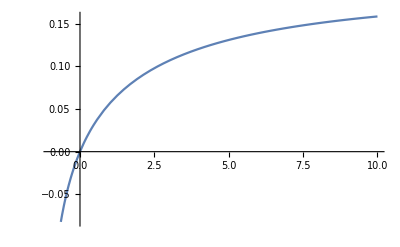

```mathematica
Plot[pfinal[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```

```mathematica
{{d11,o1},{o1,d12}}
```

{{-a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b))),0},{0,-(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2) √((a π-2 b π)/(2 a^2-6 a b)))}}

```mathematica
{{d21,o21,o22},{o21,d22,o23},{o22,o23,d23}}
```

{{-(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))+a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))),0,-(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2)+(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))},{0,-(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))),0},{-(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2)+(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))),0,-(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))}}

```mathematica
{{intd31,into31,into32,into33},{into31,intd32,into34,into35},{into32,into34,intd33,into36},{into33,into35,into36,intd34}}
```

{{(2 √(a^2 (a-3 b)))/(√a (2 a-3 b)),0,(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),0},{0,0,0,0},{(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),0,(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),0},{0,0,0,0}}

```mathematica
1-d11-d12-d21-d22-d23-intd31-intd32-intd33-intd34
```

1+(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))-(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2) √((a π-2 b π)/(2 a^2-6 a b)))

### Create Density Operator for MMRDO

```mathematica
matrixvac[a_,b_]:= 1+(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))-(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2) √((a π-2 b π)/(2 a^2-6 a b)))
```

```mathematica
matrixone[a_,b_]:={{-a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b))),0},{0,-(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) b^2)/((a-2 b) ((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) π ((2 a^2-5 a b+b^2)/(2 a π-4 b π))^(3/2) √((a π-2 b π)/(2 a^2-6 a b)))}}
```

```mathematica
matrixtwo[a_,b_]:={{-(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))+a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))),0,-(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2)+(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))},{0,-(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))),0},{-(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2)+(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))),0,-(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)+(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))}}
```

```mathematica
matrixthree[a_,b_]:={{(2 √(a^2 (a-3 b)))/(√a (2 a-3 b)),0,(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),0},{0,0,0,0},{(2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),0,(2 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),0},{0,0,0,0}}
```

```mathematica
matrixdim={{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Eigenvalues[matrixtwo[A[lp[-0.99]], B[lm,lp[-0.99],Np]]]
```

{0.0392384,0.00525699,0.000250181}

```mathematica
fullmatrix[k_]:=Fold[ArrayFlatten[{{#,0},{0,#2}}]&,matrixvac[A[lp[k]], B[lm,lp[k],Np]],{matrixone[A[lp[k]], B[lm,lp[k],Np]],matrixtwo[A[lp[k]], B[lm,lp[k],Np]],matrixthree[A[lp[k]], B[lm,lp[k],Np]], matrixdim}]
```

```mathematica
Eigenvalues[fullmatrix[50.3]]
```

{0.697285,0.199722,0.0355117,0.0351983,0.0278175,0.00428243,0.000183298,-1.38778×10^-17,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
fullmatrix[100.6] //MatrixForm
```

(0.261012 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.040442 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0378594 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0226578 | 0 | 0.0193116 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.00527522 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0193116 | 0 | 0.0168959 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.573094 | 0 | 0.156548 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.156548 | 0 | 0.0427632 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
matexportfunct[i_, ind_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/"<>"data_m01_negk"<>ToString[ind]<>".mat", fullmatrix[i]]
```

```mathematica
kappalogrange[i_]:= If[i≤1, i, 10^(i-1)]
kappamin = -0.99;
kappamax = 0;
kappagran = 0.05;
kappalist = Table[kappalogrange[k], {k,kappamin, kappamax, kappagran}];
```

```mathematica
Table[matexportfunct[kappalist[[i]],i],{i,1,Length[kappalist]}]
```

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk1.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk2.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk3.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk4.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk5.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk6.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk7.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk8.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk9.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk10.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk11.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk12.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk13.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk14.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk15.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk16.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk17.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk18.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk19.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Bosons Analytic Results/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m01/data_m01_negk20.mat}